```mathematica
Table[ a[j],{j,1,30}]
```

{1,1,1,2,1,1,1,3,2,1,1,2,1,1,1,5,1,2,1,2,1,1,1,3,2,1,3,2,1,1}

```mathematica
Clear[f]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
a[n_] := FiniteAbelianGroupCount[n]
f[n_,k_] := f[n,k]=Sum[ a[j]f[Floor[n/j],k-1],{j,2,n}]
f[n_, 0] := UnitStep[n-1]
fz[n_, z_] := Sum[ bin[z,k]f[n,k],{k,0,Log2@n}]
lf[n_] := Sum[ (-1)^(k+1)/k f[n,k],{k,1,Log2@n}]
pr[n_] := Sum[ PrimePi[n^(1/k)]/k,{k,1,Log2@n}]
pr2[n_]  := Sum[ pr[n^(1/k)],{k,1,Log2@n}]
pr2d[n_] := pr2[n]-pr2[n-1]
```

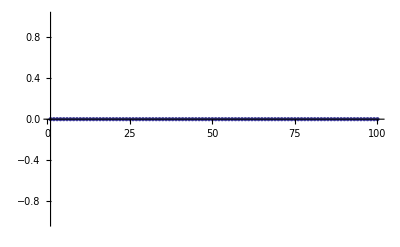

```mathematica
DiscretePlot[lf[n]-pr2[n],{n,1,100}]
```

```mathematica
Table[{n,pr2d[n]},{n,2,100}]//TableForm
```

2 | 1
3 | 1
4 | 3/2
5 | 1
6 | 0
7 | 1
8 | 4/3
9 | 3/2
10 | 0
11 | 1
12 | 0
13 | 1
14 | 0
15 | 0
16 | 7/4
17 | 1
18 | 0
19 | 1
20 | 0
21 | 0
22 | 0
23 | 1
24 | 0
25 | 3/2
26 | 0
27 | 4/3
28 | 0
29 | 1
30 | 0
31 | 1
32 | 6/5
33 | 0
34 | 0
35 | 0
36 | 0
37 | 1
38 | 0
39 | 0
40 | 0
41 | 1
42 | 0
43 | 1
44 | 0
45 | 0
46 | 0
47 | 1
48 | 0
49 | 3/2
50 | 0
51 | 0
52 | 0
53 | 1
54 | 0
55 | 0
56 | 0
57 | 0
58 | 0
59 | 1
60 | 0
61 | 1
62 | 0
63 | 0
64 | 2
65 | 0
66 | 0
67 | 1
68 | 0
69 | 0
70 | 0
71 | 1
72 | 0
73 | 1
74 | 0
75 | 0
76 | 0
77 | 0
78 | 0
79 | 1
80 | 0
81 | 7/4
82 | 0
83 | 1
84 | 0
85 | 0
86 | 0
87 | 0
88 | 0
89 | 1
90 | 0
91 | 0
92 | 0
93 | 0
94 | 0
95 | 0
96 | 0
97 | 1
98 | 0
99 | 0
100 | 0

```mathematica
Table[DirichletCharacter[3,1,n],{n,0,10}]
```

{0,1,1,0,1,1,0,1,1,0,1}

```mathematica
DirichletCharacter[3,1,16]DirichletCharacter[3,1,41]
```

1

```mathematica
DirichletCharacter[3,1,16 41]
```

1

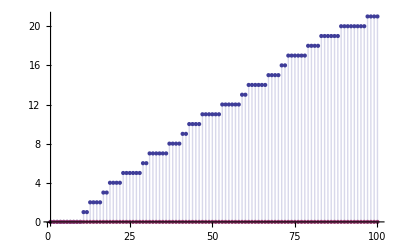

1 | 0 | 0
2 | 0 | 0
3 | 0 | 0
4 | 0 | 0
5 | 0 | 0
6 | 0 | 0
7 | 0 | 0
8 | 0 | 0
9 | 0 | 0
10 | 0 | 0
11 | 1. | 0
12 | 0 | 0
13 | 1. | 0
14 | 0 | 0
15 | 0 | 0
16 | 0 | 0
17 | 1. | 0
18 | 0 | 0
19 | 1. | 0
20 | 0 | 0

```mathematica
Clear[f]
a[n_] := DirichletCharacter[ 210,1,n]
f[n_,k_] := f[n,k]=Sum[ a[j]f[Floor[n/j],k-1],{j,2,n}]
f[n_, 0] := UnitStep[n-1]
lf[n_] := Sum[ (-1)^(k+1)/k f[n,k],{k,1,Log2@n}]
DiscretePlot[{ Re[lf[n]], Im[lf[n]]},{n,1,100}]
Table[{ n, Chop@N@Re[lf[n]-lf[n-1]],Chop@N@Im[lf[n]-lf[n-1]]},{n,1,20}]//TableForm
```

```mathematica
Table[ DirichletCharacter[210,1,n],{n,1,100}]
```

{1,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0}

```mathematica
lf[100]+1+1/2+1/3+1/4+1/5+1/6+1+1/2+1/3+1/4+1+1/2+1+1/2
```

428/15

```mathematica
Clear[aa]
ap[n_,p_] := Floor[n^(1/p)]-Floor[(n-1)^(1/p)]
aa[n_] := aa[n]=Sum[ap[j,1]ap[k,2]ap[l,3]ap[m,4]ap[o,5]ap[p,6],{j,1,n},{k,1,n/j},{l,1,n/(j k)},{m,1,n/(j k l)},{o,1,n/(j k l m)},{p,1,n/(j k l m o)}]
```

```mathematica
Table[ aa[n]-aa[n-1],{n,1,20}]
```

{1,1,1,2,1,1,1,3,2,1,1,2,1,1,1,5,1,2,1,2}

```mathematica
Table[ a[n],{n,1,20}]
```

{1,1,1,2,1,1,1,3,2,1,1,2,1,1,1,5,1,2,1,2}